### Expectation value of Marcenko–Pastur law

```mathematica
Integrate[1/(2*Pi*P)*Sqrt[(b-x)*(x-a)],{x,a,b}]
```

(√((a-b)^2) (-a+b))/(16 P)

### Expectation value of the inverse Marcenko–Pastur law

```mathematica
Integrate[1/(2*Pi*x^2)*Sqrt[(x-a)*(b-x)],{x,a,b},Assumptions->{a>0,b>0,b>a}]
```

(a+b-2 √(a b))/(4 √(a b))

### Spectrum from the Stieltjes transformation and only the second solution has the right domain.

```mathematica
solution=Solve[σ^4*z*m^3-2*σ^2*z*m+(σ^2+z-1)*m-1==0,m][[All,1,2]];
```

```mathematica
solution[[2]]
```

((1+ⅈ √3) (-1+z+σ^2-2 z σ^2))/(2^(2/3) (27 z^2 σ^8+√(729 z^4 σ^16+108 z^3 σ^12 (-1+z+σ^2-2 z σ^2)^3))^(1/3))-((1-ⅈ √3) (27 z^2 σ^8+√(729 z^4 σ^16+108 z^3 σ^12 (-1+z+σ^2-2 z σ^2)^3))^(1/3))/(6 2^(1/3) z σ^4)

```mathematica
Simplify[ComplexExpand[Im[solution[[2]]],{z, σ}∈Reals]]
```

-(((-2 z σ^4+2 z^2 σ^4+2 z σ^6-4 z^2 σ^6+2^(1/3) (27 z^4 σ^16+√(z^6 σ^24 (27 z σ^4+4 (-1+z+σ^2-2 z σ^2)^3)^2)+6 √3 z^2 σ^8 (z^6 σ^24 (27 z σ^4+4 (-1+z+σ^2-2 z σ^2)^3)^2)^(1/4) Cos[1/2 Arg[z^3 σ^12 (27 z σ^4+4 (-1+z+σ^2-2 z σ^2)^3)]])^(1/3)) (-3 Cos[1/3 Arg[27 z^2 σ^8+√(729 z^4 σ^16+108 z^3 σ^12 (-1+z+σ^2-2 z σ^2)^3)]]+√3 Sin[1/3 Arg[27 z^2 σ^8+√(729 z^4 σ^16+108 z^3 σ^12 (-1+z+σ^2-2 z σ^2)^3)]]))/(6 2^(2/3) z σ^4 (27 z^4 σ^16+√(z^6 σ^24 (27 z σ^4+4 (-1+z+σ^2-2 z σ^2)^3)^2)+6 √3 z^2 σ^8 (z^6 σ^24 (27 z σ^4+4 (-1+z+σ^2-2 z σ^2)^3)^2)^(1/4) Cos[1/2 Arg[z^3 σ^12 (27 z σ^4+4 (-1+z+σ^2-2 z σ^2)^3)]])^(1/6)))

```mathematica
Pho[z_, σ_]:=-(((-2 z σ^4+2 z^2 σ^4+2 z σ^6-4 z^2 σ^6+2^(1/3) (27 z^4 σ^16+√(z^6 σ^24 (27 z σ^4+4 (-1+z+σ^2-2 z σ^2)^3)^2)+6 √3 z^2 σ^8 (z^6 σ^24 (27 z σ^4+4 (-1+z+σ^2-2 z σ^2)^3)^2)^(1/4) Cos[1/2 Arg[z^3 σ^12 (27 z σ^4+4 (-1+z+σ^2-2 z σ^2)^3)]])^(1/3)) (-3 Cos[1/3 Arg[27 z^2 σ^8+√(729 z^4 σ^16+108 z^3 σ^12 (-1+z+σ^2-2 z σ^2)^3)]]+√3 Sin[1/3 Arg[27 z^2 σ^8+√(729 z^4 σ^16+108 z^3 σ^12 (-1+z+σ^2-2 z σ^2)^3)]]))/(6 2^(2/3) z σ^4 (27 z^4 σ^16+√(z^6 σ^24 (27 z σ^4+4 (-1+z+σ^2-2 z σ^2)^3)^2)+6 √3 z^2 σ^8 (z^6 σ^24 (27 z σ^4+4 (-1+z+σ^2-2 z σ^2)^3)^2)^(1/4) Cos[1/2 Arg[z^3 σ^12 (27 z σ^4+4 (-1+z+σ^2-2 z σ^2)^3)]])^(1/6)));
```

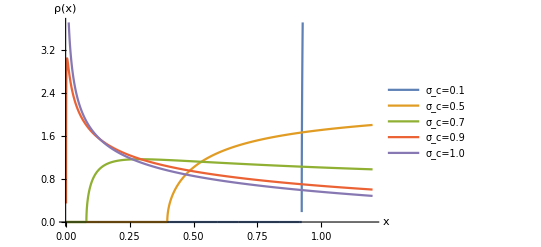

```mathematica
g=Plot[{Pho[z, 0.1],Pho[z, 0.5],Pho[z, 0.7],Pho[z, 0.9],Pho[z, 1.0]},{z,0,1.2},PlotPoints->2000,PlotLegends->Placed[{"σ_c=0.1","σ_c=0.5","σ_c=0.7","σ_c=0.9","σ_c=1.0"},{0.25,0.75}],AxesLabel->{"x","ρ(x)"}]
```

```mathematica
Export["FigS4_spectrumRMT.pdf",g]
```

FigS4_spectrumRMT.pdf

```mathematica
SystemOpen["FigS4_spectrumRMT.pdf"]
```